```mathematica
ProbSweep1D[c0_,c1_]:=(-c0+c1)/c1
ProbSweep2D[c0_,c1_]:=(3 (c0-c1)^2)/(-3 c0 (c0-2 c1)+3 (c0-c1)^2)
```

```mathematica
ProbSweep3D[c0_,c1_]:=(12 (c0-c1)^3)/(12 (c0-c1)^3-12 c0 (c0^2-3 c0 c1+3 c1^2))
```

1

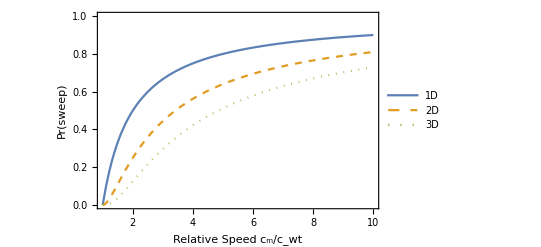

```mathematica
c0=1
Plot[{ProbSweep1D[c0,c1],ProbSweep2D[c0,c1],ProbSweep3D[c0,c1]},{c1,1,10}, PlotStyle-> {Line, Dashed, Dotted}, PlotRange->{{1,10},{0,1}}, Frame-> True, FrameLabel->{Style["Relative Speed c_m/c_wt",Bold,12], Style["Pr(sweep)",Bold,12]}, RotateLabel->True, PlotLegends->Placed[{"1D","2D","3D"},Center]]
```

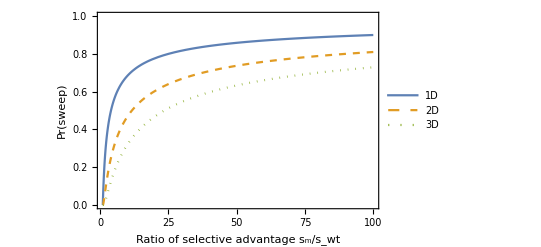

```mathematica
Plot[{ProbSweep1D[c0,Sqrt[c1]],ProbSweep2D[c0,Sqrt[c1]],ProbSweep3D[c0,Sqrt[c1]]},{c1,1,100}, PlotStyle-> {Line, Dashed, Dotted}, PlotRange->{{1,100},{0,1}}, Frame-> True, FrameLabel->{Style["Ratio of selective advantage s_m/s_wt",Bold,12], Style["Pr(sweep)",Bold,12]}, RotateLabel->True, PlotLegends->Placed[{"1D","2D","3D"},Center]]
```